# Fitting Sunspots

## Creating the Schuster Periodogram

Data imported from Royal Observatory of Belgium, Brussels at: http://www.sidc.be/silso/datafiles.

```mathematica
data = Import[NotebookDirectory[]<>"ISSN_M_tot.csv"];
```

```mathematica
time=data⟦;;,3⟧;
spots=data⟦;;,4⟧;
spots=spots-Mean[spots]; (* subtract mean to center data on zero *)
points=Table[{time⟦k⟧,spots⟦k⟧},{k,1,Length[time]}];
len=Length[points];
```

By plotting the data, we estimate the period to be T = 10 ± 3 years.

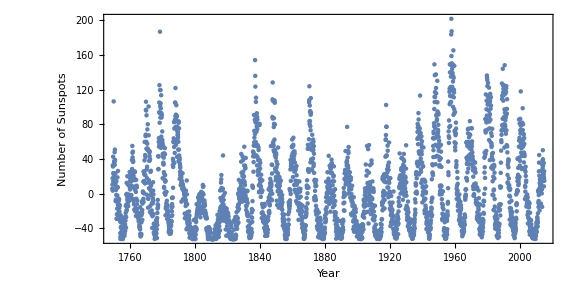

```mathematica
ListPlot[points,AspectRatio->0.5,ImageSize->Large,BaseStyle->{FontFamily->"Times New Roman",FontSize->12,FontColor->Black},Frame->{{True,False},{True,False}},FrameLabel->{"Year", "Number of Sunspots"}]
```

Next, we define the Schuster Periodogram: c(ω).

```mathematica
c[ω_]:=1/len^2(Abs[Total[spots Exp[ⅈ ω time]]])^2;
```

We find that our estimate of T = 10±3 years ω = {0.483, 0.898}

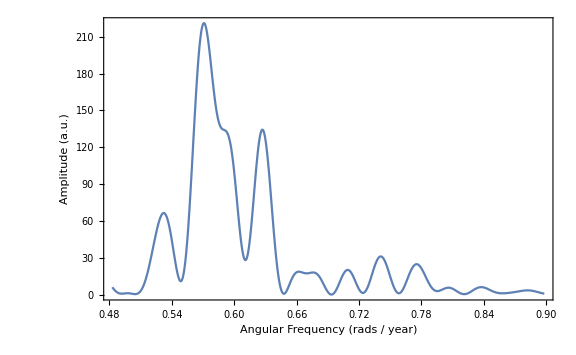

```mathematica
Plot[c[x],{x,0.483,0.898},PlotRange->All, Frame->{{True,False},{True,False}},FrameLabel->{"Angular Frequency (rads / year)", "Amplitude (a.u.)"}, ImageSize->Large]
```

This plot shows that there is a clear maximum around ω = 0.57

## Finding the Maximum Frequency

### Comparing methods of finding frequency

```mathematica
ω0Newton=Quiet@Reap[FindMaximum[c[ω],{ω,0.6},Method->"Newton",StepMonitor:>Sow[ω]]];
ω0Principle=Quiet@Reap[FindMaximum[c[ω],{ω,0.6},Method->"PrincipalAxis",StepMonitor:>Sow[ω]]];
ω0Conjugate = Quiet@Reap[FindMaximum[c[ω],{ω,0.6},Method->"ConjugateGradient",StepMonitor:>Sow[ω]]];
```

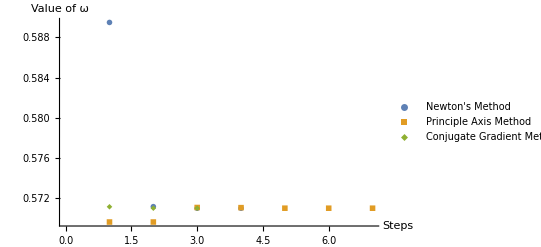

```mathematica
ListPlot[{ω0Newton⟦2,1⟧ ,ω0Principle⟦2,1⟧,ω0Conjugate⟦2,1⟧},PlotRange->All,PlotMarkers->{Automatic,  Medium},PlotLegends->{"Newton's Method","Principle Axis Method","Conjugate Gradient Method"}, AxesLabel->{"Steps", "Value of ω"}]
```

All of the methods require a small number of steps.  We can see that Newton’s method converges quickly compared to the Principle Axis method, but slightly slower than the Conjugate Gradient Method.  However, Newton’s method was the only one that didn’t return some error, so it might be the the best method given the circumstances.

### Determine frequency with maximum “response” and fit the data to a model

To find the maximum frequency, we plug in our visual estimate of the peak ω = 0.57  to the findMaximum function.

```mathematica
ω0=ω/.Last[FindMaximum[c[ω],{ω,0.57}]] (* frequency (rad/year) *)
```

0.571033

Our initial plot of the spots shows sinusoidal behavior, so we fit to the function A Cos[ω0 t + ϕ]  and use FindFit to obtain the values of A and ϕ.

```mathematica
model=A Cos[ω0 t+ϕ];
fit=FindFit[points, model,{A,ϕ},t]
```

{A→29.5564,ϕ→-0.314746}

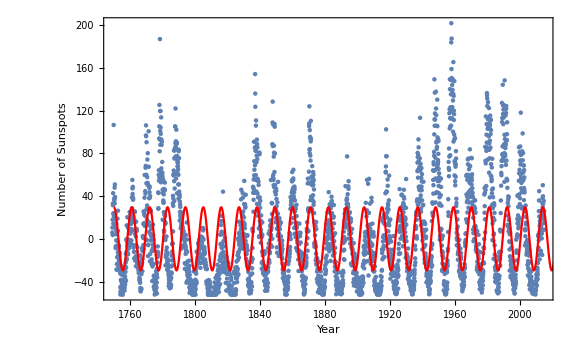

```mathematica
Show[{ListPlot[points],Plot[model/.fit,{t,1750,2500},PlotStyle->Red]},ImageSize->Large,Frame->{{True, False},{True, False}},FrameLabel->{"Year", "Number of Sunspots"}]
```

Plotting the model against the data shows us that the model seems to be a good fit, we verify this by looking at the noise and checking the residuals.

```mathematica
residual=Table[{time⟦k⟧,spots⟦k⟧-model/.fit/.t->time⟦k⟧},{k,1,len}];
noise=Table[spots⟦k⟧-model/.fit/.t->time⟦k⟧,{k,1,len}];
```

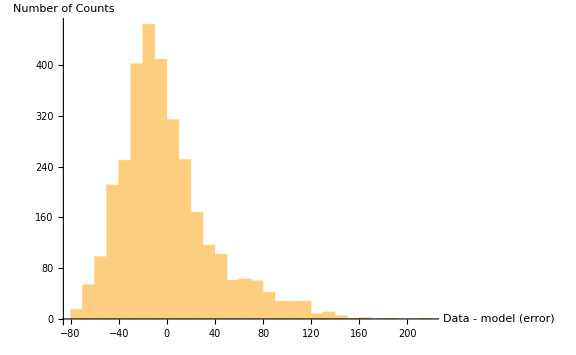

```mathematica
Histogram[noise, AxesLabel->{"Data - model (error)", "Number of Counts"},ImageSize->Large]
```

The noise shows a roughly Boltzmann like distribution. However, for ease, we will approximate it as Gaussian, which will overestimate rather than underestimate the error.

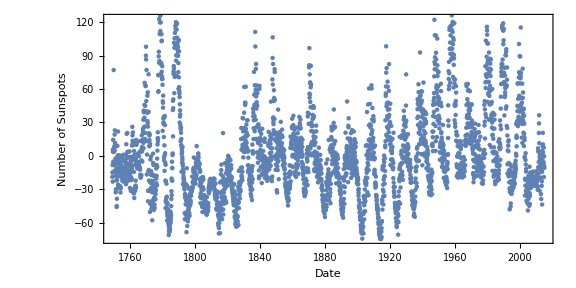

```mathematica
ListPlot[residual,Frame->{{True, False},{True, False}}, FrameLabel->{"Date", "Number of Sunspots"},AspectRatio->0.5,ImageSize->Large]
```

The residual shows a clear sinusoidal shape, hinting that there are lower frequency terms that could be added to our model. This will be explored later.

## Find the Confidence Interval

### Determine likeliness function

```mathematica
σ=StandardDeviation[noise];
```

We consider region centered at ω0 from [0.2, 2 ω0 - 0.2] to cut out the low frequency ω < 0.2 noise.

```mathematica
P[ω_]:=Exp[c[ω]/σ^2]-1;
normalizationFactor=NIntegrate[P[ω],{ω,0.2,2ω0-0.2}];
normalizedP[ω_]:=P[ω]/normalizationFactor;
```

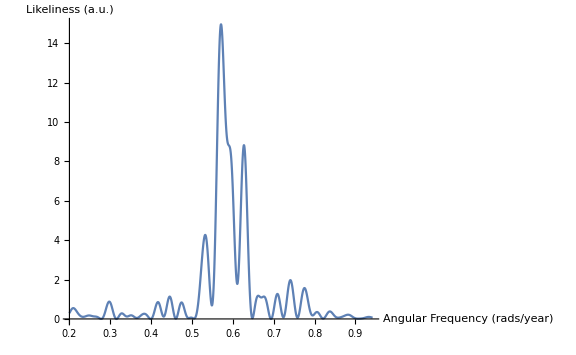

```mathematica
Plot[normalizedP[ω],{ω,0.2,2ω0-0.2},PlotRange-> All,AxesLabel->{"Angular Frequency (rads/year)", "Likeliness (a.u.)"},ImageSize->Large]
```

We define a function which returns the area under the curve in the region [ω0 - δω, ω0 + δω]

```mathematica
confidenceInterval[δω_?NumberQ]:= NIntegrate[normalizedP[ω],{ω,ω0-δω,ω0+δω}];
(* find interval for which 95% of area is covered *)
δω = δω/.FindRoot[confidenceInterval[δω]-0.95,{δω,0.24,0.25},Method->"Brent"]
```

0.24318

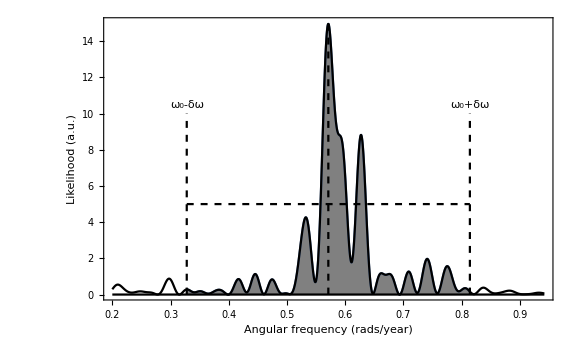

```mathematica
Show[{
Plot[normalizedP[ω],{ω,ω0-δω,ω0+δω},Filling->Bottom,FillingStyle->Gray, PlotRange->{{0.2,2ω0-0.2},All},PlotPoints->100],Plot[normalizedP[ω],{ω,0.2,2ω0-0.2},PlotRange->All,PlotStyle->Black],
ListPlot[{{{ω0-δω,0},{ω0-δω, 10}},{{ω0,0},{ω0,15}},{{ω0+δω,0},{ω0+δω,10}},{{ω0-δω,5},{ω0+δω,5}},{{0.2,0},{2ω0-0.2,0}}},
Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black}}],
Graphics[{Text["ω_0+δω",{ω0+δω,10.5}],Text["ω_0-δω",{ω0-δω,10.5}]}]
},ImageSize->Large,
Frame->{{True, False},{True, False}},
FrameStyle->Black,
FrameLabel->{"Angular frequency (rads/year)", "Likelihood (a.u.)"},
BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

We find that, with 95% confidence, ω ∈ {0.3279, 0.8142}

## Looking into Low Frequency Response

We saw that the residual had a clear sinusoidal shape, indicating that adding lower frequency sine or cosine terms could improve the fit.  We do this by first looking for the local maximum response for a frequency less than ω0 previously found.

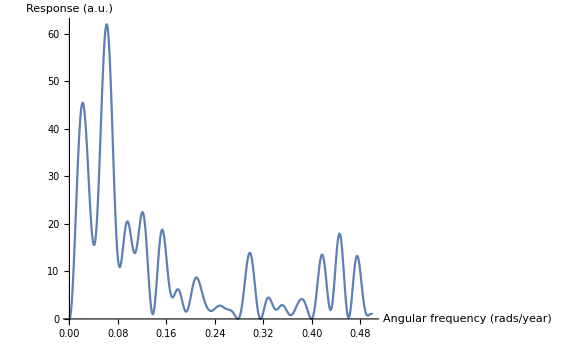

```mathematica
Plot[c[ω],{ω,0,0.5}, PlotRange->All, AxesLabel->{"Angular frequency (rads/year)", "Response (a.u.)"}, ImageSize->Large]
```

There is a particularly strong peak between 0.04 and 0.08

```mathematica
ω1=ω/.Last@FindMaximum[c[ω],{ω,0.04,0.08}];
```

```mathematica
model2 =A0 Cos[ω0 t + ϕ0] + A1 Cos[ω1 t + ϕ1] ;
fit2 = FindFit[points, model2, {A0,A1,ϕ0,ϕ1}, t];
```

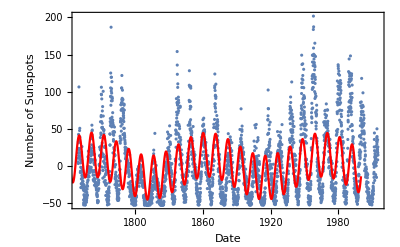

```mathematica
Show[ListPlot[points],Plot[model2/.fit2,{t,1700,2000},PlotStyle->Red],Frame->{{True, False},{True, False}},FrameLabel->{"Date", "Number of Sunspots"}]
```

Notice that this fit appears much better at capturing the slowly varying changes in the data, which we will verify by studying the residuals.

```mathematica
noise2=spots-Table[model2/.fit2/.t->time⟦k⟧,{k,1,len}];
residual2=Table[{time⟦k⟧,noise2⟦k⟧},{k,1,len}];
```

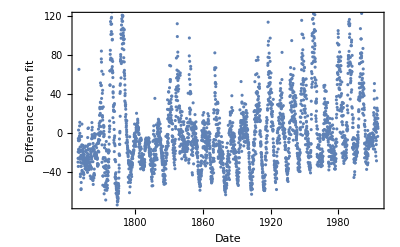

```mathematica
ListPlot[residual2,Frame->{{True, False},{True, False}},FrameLabel->{"Date", "Difference from fit"}]
```

Much of the slow variation has been been removed, and the residual appears qualitatively more “random.”  However there does appear to still be some sinusoidal behavior.

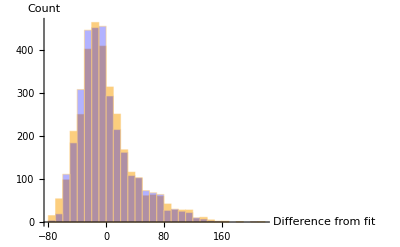

```mathematica
Show[Histogram[noise],Histogram[noise2,ChartStyle->{Directive[Blue,Opacity[0.3]]}],AxesLabel->{"Difference from fit", "Count"}]
```

Interestingly, the noise is much the same as before, with not as much of a reduction as expected.

```mathematica
σ2=StandardDeviation[noise2]
```

37.1321

Conclusions: The standard deviation of the noise with the additional cosine term was indeed smaller, but only by a very small amount: 37.13 vs 38.74. The additional cosine term captures some of the slower periodic shapes in the data, but it is not drastically changing the fit as a whole, and certainly is not changing the most noticeable periodicity which was measured in the first few sections of this notebook.